1-D animation

```mathematica
omega=1;
rad=0.1;
len=1;
x0=0; xf=8; y0=0; yf=2;
thetarange=Range[0,omega* 10,1/10];

movievector =ConstantArray[0,Length[thetarange]];
For[t=1,t<Length[thetarange],t++,

x1=-3.5+2*thetarange[[t]]; y1=0.25; 
x2=-5+2*thetarange[[t]]; y2=1.25;
x3=-7+2*thetarange[[t]]; y3=0.35;
x4=-12+2*thetarange[[t]]; y4=1.15;
x5=-16.5+2*thetarange[[t]]; y5=0.65;
x6=-17+2*thetarange[[t]]; y6=0.75;

x11=-1.5+2*thetarange[[t]]; y11=1.25; 
x12=-3.5+2*thetarange[[t]]; y12=0.55;
x13=-4.5+2*thetarange[[t]]; y13=1.35;
x14=-5.5+2*thetarange[[t]]; y14=0.15;
x15=-6.5+2*thetarange[[t]]; y15=0.65;
x16=-7+2*thetarange[[t]]; y16=0.75;
movievector[[t]]=Show[
DensityPlot[ Pi x,{x,x0,xf},{y,y0,yf},{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase- thetarange[[t]]]/2,0.5+Sin[phase- thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->{True,False}, ImageSize->Large,PlotPoints->200],

Graphics[{Thickness[0.001],White,Circle[{x1,y1},rad+.01]}],Graphics[{Thick,White,Circle[{x1,y1},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x2,y2},rad+.01]}],Graphics[{Thick,White,Circle[{x2,y2},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x3,y3},rad+.01]}],Graphics[{Thick,White,Circle[{x3,y3},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x4,y4},rad+.01]}],Graphics[{Thick,White,Circle[{x4,y4},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x5,y5},rad+.01]}],Graphics[{Thick,White,Circle[{x5,y5},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x6,y6},rad+.01]}],Graphics[{Thick,White,Circle[{x6,y6},rad]}],


Graphics[{Thickness[0.001],White,Circle[{x11,y11},rad+.01]}],Graphics[{Thick,White,Circle[{x11,y11},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x12,y12},rad+.01]}],Graphics[{Thick,White,Circle[{x12,y12},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x13,y13},rad+.01]}],Graphics[{Thick,White,Circle[{x13,y13},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x14,y14},rad+.01]}],Graphics[{Thick,White,Circle[{x14,y14},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x15,y15},rad+.01]}],Graphics[{Thick,White,Circle[{x15,y15},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x16,y16},rad+.01]}],Graphics[{Thick,White,Circle[{x16,y16},rad]}]

]]

fileName="1Danimation_new.avi";
Export[fileName,movievector];
Directory[];
```

-Graphics-

```mathematica
rad=0.1;
len=1;
x0=0; xf=8; y0=0; yf=2;
x1=1.5; y1=0.25; 
x2=3.5; y2=1.25;
x3=4.5; y3=0.35;
x4=5.5; y4=1.15;
x5=6.5; y5=0.65;
x6=7; y6=0.75;
Show[
DensityPlot[ Pi x,{x,x0,xf},{y,y0,yf},{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->{True,False}, ImageSize->Large,PlotPoints->200],

Graphics[{Thickness[0.001],White,Circle[{x1,y1},rad+.01]}],Graphics[{Thick,White,Circle[{x1,y1},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x2,y2},rad+.01]}],Graphics[{Thick,White,Circle[{x2,y2},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x3+1,y3},rad+.01]}],Graphics[{Thick,White,Circle[{x3,y3},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x4,y4},rad+.01]}],Graphics[{Thick,White,Circle[{x4,y4},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x5,y5},rad+.01]}],Graphics[{Thick,White,Circle[{x5,y5},rad]}],

Graphics[{Thickness[0.001],White,Circle[{x6,y6},rad+.01]}],Graphics[{Thick,White,Circle[{x6,y6},rad]}]

]
```

-Graphics-

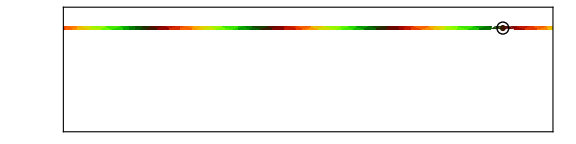

```mathematica
x0=7.3; y0=1.7;
Show[
 
DensityPlot[ Pi x,{x,y}∈Disk[{x0,y0},rad+.05],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotRange->{{0,8},{0,2}}],
Graphics[{Thickness[0.01],White,Circle[{x0,y0},rad+.02]}],
DensityPlot[ Pi x,{x,y}∈Rectangle[{x0-len,y0-rad/4},{x0+len,y0+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x0,y0},rad]}]]
```

```mathematica
x0=7.3; y0=1.7;
Show[
 
Plot[ Pi x,{x,y}∈Disk[{x0,y0},rad+.05],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotRange->{{0,8},{0,2}}]]
```

Plot::idomdim: {x,y}∈Disk[{x0,y0},rad+0.05] does not have a valid dimension as a plotting domain.

Show::gtype: Plot is not a type of graphics.

Show[Plot[π x,{x,y}∈Disk[{x0,y0},rad+0.05],{ColorFunction→Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling→False,AspectRatio→1/4,Frame→True,FrameTicks→False,ImageSize→Large,PlotRange→{{0,8},{0,2}}]]